78539.8

0.127386

7.58981-0.697546 ⅈ

7.58981-0.697546 ⅈ

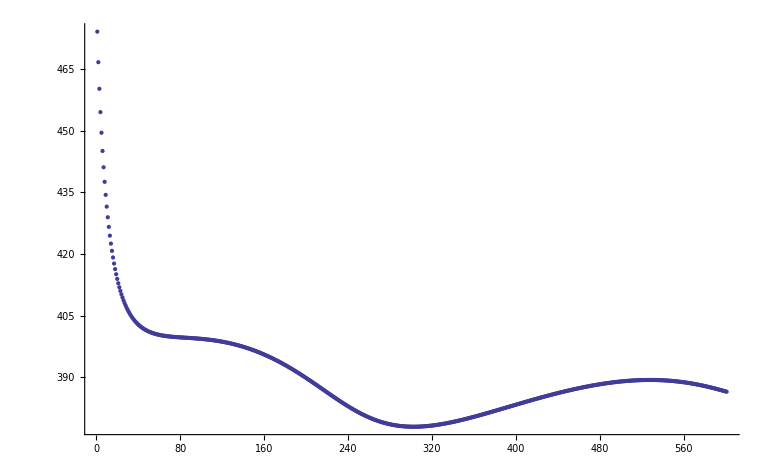

res_a.txt

```mathematica
(* Clear all data before calculations *)
Clear[r, x, r12, r21, r34, r43, z, r13, r31, r24, r42, diag, r14, r41, r23, r32, clight, ωp, fp, γ, sol, M, nsubstrate];

(* Geometry parameters of ellipsoid *)
Clear[a, b, c, V, L1];
a = 50; (* 1/2 Length *)
b = 25; (* 1/2 Width *)
c = 15;  (* 1/2 Height *)
V = N[4/3 π a b c]
L1 = NIntegrate[a b c / (2 (s+ a^2 )^(3/2) (s + b^2)^(1/2) (s + c^2)^(1/2)), {s, 0, Infinity}]


(* Distance btw nanorods *)
z = 30;
r = z;

(* Constants [nm/fs] *)
nsubstrate =1.4; 
clight = 300;
fp =2.183;  (* plasma frequency of gold in 1/fs *)
ωp = 2π fp;
a = 10;
γ =0 6.46*10^(-3);


(* Drude model & phys functions *)
ϵ[ω_] := 1- ωp^2/(ω^2+ ⅈ γ ω);
α[ω_] := V/(4 3.1415 (L1+ 1/(ϵ[ω]-1))); 
k[ω_] :=ω/clight ;

(* Define tensor components *)

χ[ω_] := Exp[ⅈ k[ω] r] /r * (k[ω]^2 + ⅈ k[ω] /r - 1/r^2);

(* Finding resonance frequencies *)

FindRoot[1/α[ω] - χ[ω] == 0, {ω, .4}][[1]][[2]]
FindRoot[χ[ω] - 1/α[ω] == 0, {ω, .4}][[1]][[2]]

(* Symmetrical mode *)
Clear[ω, sol1, w, z, listYs, listX, lambda];
listX = {};
listYs = {};
Do[z = i;
r = z;
AppendTo[listX, N[z]];
sol1 = FindRoot[χ[ω] + 1/α[ω] == 0, {ω, .6}][[1]][[2]];
w = Abs[sol1];
lambda = 2 π clight/ w;
AppendTo[listYs, lambda], {i, 50,650, 1}];
ListPlot[{listYs}, PlotRange -> All]

Export["res_a.txt",listYs,"Table"]
(* Export["res_a50.txt",listYs50,"Table"]
Export["res_a100.txt",listYs100,"Table"]
Export["res_a150.txt",listYs150,"Table"]
Export["res_a200.txt",listYs150,"Table"] *)
```

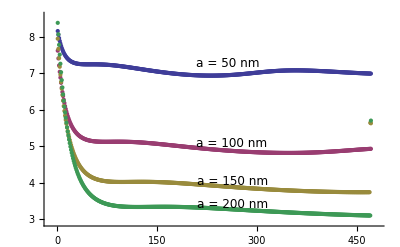

res_s.txt

res_a.txt